sWLC from Li et at, 2020
Re-viewing calculation
Lossless first, then lossy
ω_s=κ, re-labelled to align with degenerate internal squeezing

```mathematica
(*sensitivity curve, using values from Fig.4-5 in Li et al, 2020
they choose to plot ((2 α^2 Subscript[S, h])/Subscript[γ, R])^(1/2)*)
Clear[α,χ,κ,γR];
α=1;
γR=2π 500 (*Hz*);
κ=10γR;
ωs=κ;(*re-labelled to align with degenerate internal squeezing*)
Sh[Ω_,χ_]:=((Ω^2+χ^2-ωs^2)^2+Ω^2 γR^2)/(4 α^2 ωs^2 γR)
ASDh[Ω_,χ_]:=Abs[Sh[Ω,χ]]^(1/2)
(* single-mode detector, i.e. no SRC
ASDScon[Ω_]:=((Ω^2+γR^2)/(4 α^2 γR) )^(1/2)
Tcon[Ω_]:=Abs[(-2I α γR^(1/2))/(Ω+I γR) ]
Rcon[Ω_]:=Abs[(Ω-I γR)/(Ω+I γR) ]*)
(* not necessary to explicitly have anymore, just set loss and sqz to zero
ASDScon[Ω_]:=(((Ω^2-ωs^2)^2+Ω^2 γR^2)/(4 α^2 ωs^2 γR) )^(1/2)
Tcon[Ω_]:=Abs[((-2α ωs γR^(1/2))/(-I Ω))/(γR-I Ω+ωs^2/(-I Ω))](*from deg.int.sqz. limit: Abs[(2 (κaqout)^(1/2)ws G)/((κaqout-I Ω)(-I Ω)+ws^2)]*)
Rcon[Ω_]:=Abs[(-γR-I Ω+ωs^2/(-I Ω))/(γR-I Ω+ωs^2/(-I Ω))](*from deg.int.sqz. limit: Abs[(κaqout+I Ω-ws^2/(-I Ω))/(κaqout-I Ω+ws^2/(-I Ω))]*)

(*comparison:
γBaseline=ωs^2/γR;
LogLogPlot[{((Ω^2+γR^2)/(4 α^2 γR) )^(1/2),(((Ω^2-ωs^2)^2+Ω^2 γR^2)/(4 α^2 ωs^2 γR) )^(1/2),((γBaseline^2+Ω^2)/(4 α^2 γBaseline) )^(1/2)},{Ω,10,10^7},PlotLegends->"Expressions"]
-Graphics-;*)
*)
(*Labeled[LogLogPlot[{
(2/γR)^(1/2)ASDScon[ΩtoγR γR],
(2/γR)^(1/2)ASDh[ΩtoγR γR,χ=0],
(2/γR)^(1/2)ASDh[ΩtoγR γR,χ=0.995ωs],
(2/γR)^(1/2)ASDh[ΩtoγR γR,χ=ωs]},{ΩtoγR,0.15,35},ImageSize->400,PlotRange->{0.01,100},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless stable nondegenerate 3-mode amplification (sWLC)\nfor different nondegenerate gains χ\nκ=10γ_R, γ_R is SRM coupling rate",PlotStyle->{Dashed,,,}],{"angular freq, Ω/γ_R / [1/γ_R]Hz (log scale)","strain sensitivity (NSR), ((2SuperscriptBox[α, 2]SubscriptBox[S, h])/γ_R)^(1/2)\n/ [α/γ_R^(1/2)]Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]*)
(*y-axis looks all wrong because we have scaled to α*)
(*Labeled[LogLogPlot[{
ASDScon[2π f],
ASDh[2π f,χ=0],
ASDh[2π f,χ=0.995ωs],
ASDh[2π f,χ=ωs]},{f,10/(2π),10^5/(2π)},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless stable nondegenerate 3-mode amplification (sWLC)\nfor different nondegenerate gains χ\nκ=10γ_R, γ_R is SRM coupling rate",PlotStyle->{Dashed,,,}],{"frequency, f=Ω/(2 π) / Hz (log scale)","strain sensitivity (NSR), (α^2S_h)^(1/2)\n/ [α]Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]*)
Print["[old plot commented out]"]
```

[old plot commented out]

```mathematica
(*want to plot Sh^(1/2) against f using real values, to compare to sensitivity target
(recreating Fig.5 in Li et al, 2020 also requires radiation pressure noise, not yet derived)
This requires using the correct Subscript[α, GW] scale*)
Clear[α,χ,ωs,γR];
c=3 10^8(*ms^-1*);
ℏ=1 10^-34(*Js*);
Larm=4 10^3(*m*);
Pcirc=3 10^6(*J/s*);
λ0=2 10^-6(*m*);
ω0=2π c/λ0;
(*value in Li et al doesn't make sense dimensionally, using Korobko et al 2019 instead
α=((2Pcirc ℏ ω0)/(c Larm))^(1/2);*)
α=((2Pcirc Larm ω0)/(ℏ c))^(1/2);
γR=2π 500 (*Hz*);
ωs=10γR;(*=κ, re-labelled*)
(*Labeled[LogLogPlot[{
ASDScon[2π f],
ASDh[2π f,χ=0],
ASDh[2π f,χ=0.986ωs],
ASDh[2π f,χ=ωs]},{f,10,10^4},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless stable nondegenerate 3-mode amplification (sWLC)\nfor different nondegenerate gains χ\nκ=10γ_R, γ_R is SRM coupling rate\nno radiation pressure effects\nparameters of LIGO Voyager",PlotStyle->{Dashed,,,}],{"frequency, f=Ω/(2 π) / Hz (log scale)","strain sensitivity (NSR), S_h^(1/2)\n/ Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]*)
Print["[old plot commented out]"]
```

[old plot commented out]

Lossy sensitivity, adding loss terms to each mode, assuming each noise is quantum with uncorrelated vacuum bath

```mathematica
(*semi-automated plotting*)
(*separating losses and making transmittivities inputs*)
(*values are: χ, Tla, Tlb, Tlc, Rpd*)
τRoundTripArm=(2 Larm)/c;
γa[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
(*Assuming LIGO Voyager's Subscript[T, SRM] was used for γR
this is different to above for the threshold plots where I assumed the LIGO value of 56m was used for Subscript[L, SRC]*)
Tsrm=0.046;
τRoundTripSRC=-1/(2 γR)Log[1-Tsrm];(*Subscript[γ, R]=-1/(2 τRoundTripSRC)Log[1-Tsrm]*)
γb[Tlb_]:=-1/(2 τRoundTripSRC)Log[1-Tlb]
γbtot[Tlb_]:=γR+γb[Tlb]
(*assuming that c mode is also in SRC, e.g. non-degenerate internal squeezing*)
γc[Tlc_,symSRM_:False]:=If[symSRM,γR+-1/(2 τRoundTripSRC)Log[1-Tlc],-1/(2 τRoundTripSRC)Log[1-Tlc]]
(*symSRM=True: i.e. γctot[Tlc_]:=γR+γc0[Tlc], symmetric SRM loss assumption*)
(*signal and noise transfer functions:
Subscript[S, h]=(|R|^2+...+|Rc|^2)/(|T|^2), plot Subscript[S, h]^(1/2)=((|R|^2+...+|Rc|^2)^(1/2))/(|T|). Here, |T| and (|R|^2+...+|Rc|^2)^(1/2)*)
TsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=(1-Rpd)^(1/2)Abs[((-2α ωs γR^(1/2))/(γa[Tla]-I Ω))/(γbtot[Tlb]-I Ω+ωs^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω))]
RsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=((1-Rpd)(
Abs[γbtot[Tlb]-2γR-I Ω+ωs^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]^2
+Abs[(-2(γR γa[Tla])^(1/2)ωs)/(γa[Tla]-I Ω)]^2
+Abs[-2(γR γb[Tlb])^(1/2)]^2
+Abs[(2(γR γc[Tlc,symSRM])^(1/2)χ)/(γc[Tlc,symSRM]-I Ω)]^2)/Abs[γbtot[Tlb]-I Ω+ωs^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]^2+Rpd)^(1/2)
ASDShsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=(1/((γc[Tlc,symSRM]^2+Ω^2)4 α^2 ωs^2 γR)(
((γbtot[Tlb]-2γR)(γa[Tla] γc[Tlc,symSRM]-Ω^2)-(γa[Tla]+γc[Tlc,symSRM])Ω^2+ωs^2 γc[Tlc,symSRM]-χ^2 γa[Tla])^2
+Ω^2(χ^2-ωs^2-(γbtot[Tlb]-2γR)(γa[Tla]+γc[Tlc,symSRM])-γa [Tla]γc[Tlc,symSRM]+Ω^2)^2
+4γR γa[Tla] ωs^2(γc[Tlc,symSRM]^2+Ω^2)
+4γR γb[Tlb](γa[Tla]^2+Ω^2)(γc[Tlc,symSRM]^2+Ω^2)
+4γR γc[Tlc,symSRM] χ^2(γa[Tla]^2+Ω^2)
+Rpd/(1-Rpd)((γbtot[Tlb](γa[Tla] γc[Tlc,symSRM]-Ω^2)-(γa[Tla]+γc[Tlc,symSRM])Ω^2+ωs^2 γc[Tlc,symSRM]-χ^2 γa[Tla])^2
+Ω^2(χ^2-ωs^2-γbtot[Tlb](γa[Tla]+γc[Tlc,symSRM])-γa [Tla]γc[Tlc,symSRM]+Ω^2)^2)))^(1/2)

(*plotting*)
(*vals={χ, Tla, Tlb, Tlc, Rpd}*)
labeller[vals_,symSRM_:False]:=(
paddedStrings=StringPadRight[{ToString[N[vals[[1]]/ωs]],ToString[vals[[2]]],ToString[vals[[3]]],ToString[vals[[4]]],ToString[vals[[5]]]},4];
If[symSRM,
Style[StringForm["χ/ωs=``; T_(l, a)=``, T_(l, b)=``, γ_(c, tot)=γ_R+γ_(c, loss port)(T_(l, c)=``), R_PD=``",
paddedStrings[[1]],
paddedStrings[[2]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]]],FontFamily->"Monospace"],
Style[StringForm["χ/ωs=``; T_(l, a)=``, T_(l, b)=``, T_(l, c)=``, R_PD=``",
paddedStrings[[1]],
paddedStrings[[2]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]]],FontFamily->"Monospace"]]
(*search for mono-spaced fonts in: $FontFamilies*)
)
plotsWLC[valsList_,plotLabel_:None,plotStyle_:{},symSRM_:False]:=(
p1=LogLinearPlot[Evaluate[Table[20Log10[RsWLC@@Join[{2π f},valsList[[i]],{symSRM}]],{i,1,Length[valsList]}]]
,{f,10,10^4},ImageSize->350,PlotLegends->LineLegend[Table[labeller[valsList[[i]],symSRM],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],
ImagePadding->{{100,10},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^4},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"shot noise transfer function,\n|R| / dB (20log10)",},{,If[ToString[plotLabel]==ToString[None],ToString["optical stable WLC"],plotLabel]}}];
p2=LogLogPlot[Evaluate[Table[TsWLC@@Join[{2π f},valsList[[i]],{symSRM}],{i,1,Length[valsList]}]],{f,10,10^4},ImageSize->350,PlotLegends->LineLegend[Table[labeller[valsList[[i]],symSRM],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],ImagePadding->{{100,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{10,10^4},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}}];
p3=LogLogPlot[Evaluate[Join[
Table[ASDShsWLC@@Join[{2π f},valsList[[i]],{symSRM}],{i,1,Length[valsList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,10,10^4},ImageSize->350,ImagePadding->{{100,10},{50,1}},PlotLegends->LineLegend[Join[Table[labeller[valsList[[i]],symSRM],{i,1,Length[valsList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],PlotStyle->If[plotStyle=={},Join[Table[,{n,1,Length[valsList]}],{Directive[Red,DotDashed]}],Join[plotStyle,{Directive[Red,DotDashed]}]],PlotRange->{{10,10^4},All},Filling->{Length[valsList]+1->Bottom},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",}}];
Column[{p1,p2,p3},Spacings->0])
(*PlotStyle->{Directive[Gray,DotDashed],Gray,,Dashed,,Dashed,Directive[DotDashed,Red]}*)
```

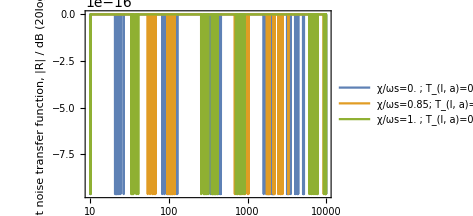
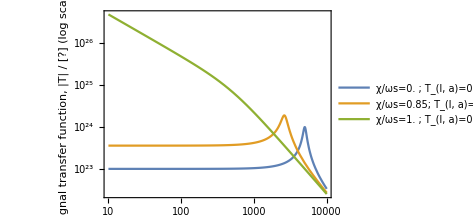
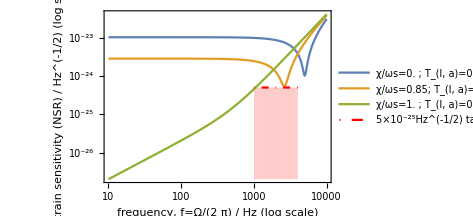

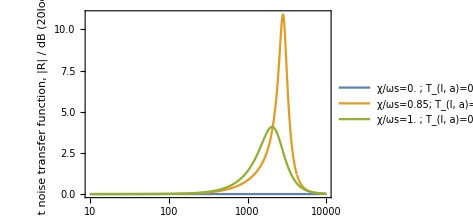
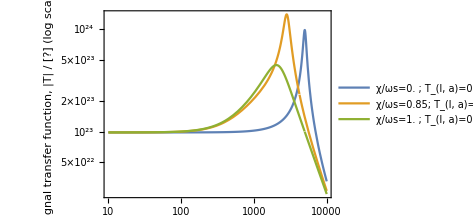
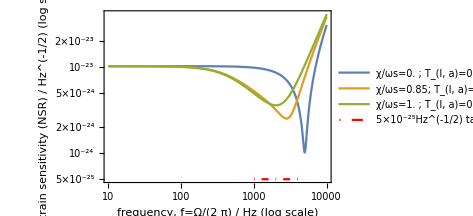

```mathematica
χRatio0=0.85;
(*values are: χ, Tla, Tlb, Tlc, Rpd*)
valsList0={{0,0,0,0,0},
{χRatio0 ωs,0,0,0,0},
{1.ωs,0,0,0,0}};
plotsWLC[valsList0]
plotsWLC[valsList0,"optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nparameters of LIGO Voyager\nno radiation pressure effects",
{},True](*with sym SRM*)
(*{{0ωs,0,0,0,0},
{χRatio0 ωs,0,0,0,0},
{χRatio0 ωs,0.1,0,0,0},
{χRatio0 ωs,0,0.1,0,0},
{χRatio0 ωs,0,0,0.1,0},
{χRatio0 ωs,0,0,0,0.5}};*)
```

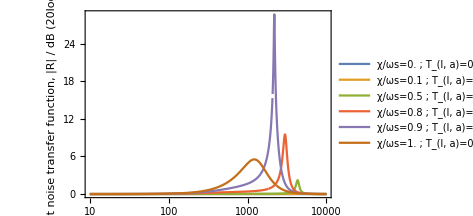
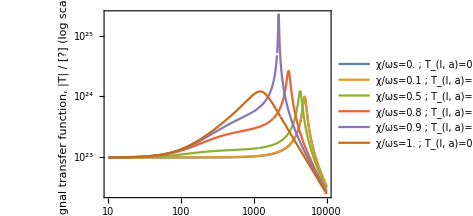
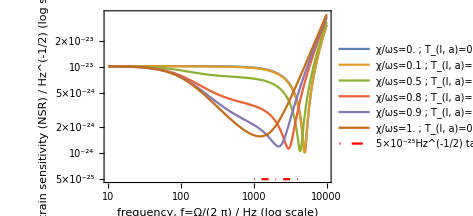

```mathematica
(*values are: χ, Tla, Tlb, Tlc, Rpd*)
Tlc0=1. 10^-2;
valsList0={
{0,0,0,Tlc0,0},
{0.1 ωs,0,0,Tlc0,0},
{0.5 ωs,0,0,Tlc0,0},
{0.8 ωs,0,0,Tlc0,0},
{0.9 ωs,0,0,Tlc0,0},
{ωs,0,0,Tlc0,0}};
plotsWLC[valsList0]
(*the effect of Tlc on threshold*)
```

```mathematica
(*optimisation via μtrics*)
(*copying from degIntSqz.nb*)
{f0, f1} = {1 10^3,4 10^3};(*Hz*)
ASDShCrit = 5 10^-25;(*Hz^(-1/2)*)
ShCrit=ASDShCrit^2;(*Hz^-1*)
μtricK[fnSh_,K_]:=1/(f1-f0)NIntegrate[(1/fnSh[2π f]-1/ShCrit)/(1/ShCrit)K[f],{f,f0,f1}]
printμtricK[fnSh_,K_]:=Print[StringForm["For S_h(Ω) given by: ``\nK=``\n--> μtricK=`` (unitless)",fnSh,K,NumberForm[μtricK[fnSh,K]]]]
μtric1[fnSh_]:=μtricK[fnSh,1&]
(*use k1=1/9 in order for Z=10 Subscript[Z, 0] to correspond to K=1/ⅇ*)
KExpk1[fnSh_,f_,k1_:1/9]:=(
Z=(1/fnSh[2π f]-1/ShCrit)/(1/ShCrit);
If[Z>0,Exp[-k1 Z],1])
μtricExpk1[fnSh_,k1_:1/9]:=μtricK[fnSh,KExpk1[fnSh,#,k1]&]
(*//end of copied code*)

(*

(*symSRM=False throughout,
to-do: try with symSRM=True*)
reduSh1[Ω_?NumericQ,r_?NumericQ]:=ASDShsWLC[Ω,r ωs,0,0,0,0]^2
opti1Fn[r_?NumericQ]:=μtric1[reduSh1[#,r]&]
opti1Vals=FindMaximum[{opti1Fn[r],0<r<1},r]
printμtricK[reduSh1[#,r/.opti1Vals[[2]][[1]]]&,1&]

k11=1/9;
optiExpk1Fn[r_?NumericQ]:=μtricExpk1[reduSh1[#,r]&,k11]
optiExpk1Vals1=FindMaximum[{optiExpk1Fn[r],0<r<1},r]
reduSh1Opti=reduSh1[#,r/.optiExpk1Vals1[[2]][[1]]]&
printμtricK[reduSh1Opti,KExpk1[reduSh1Opti,#,k11]&]

k12=100;
optiExpk1Fn[r_?NumericQ]:=μtricExpk1[reduSh1[#,r]&,k12]
optiExpk1Vals2=FindMaximum[{optiExpk1Fn[r],0<r<1},r,MaxIterations->5]
reduSh1Opti=reduSh1[#,r/.optiExpk1Vals2[[2]][[1]]]&
printμtricK[reduSh1Opti,KExpk1[reduSh1Opti,#,k12]&]
-Graphics-;
(*optimisation finds values off threshold*)
plotsWLC[{
{0ωs,0,0,0,0},
{(r/.opti1Vals[[2]][[1]]) ωs,0,0,0,0},
{(r/.opti1Vals[[2]][[1]]) ωs,0.1,0,0,0},
{(r/.optiExpk1Vals1[[2]][[1]]) ωs,0,0,0,0},
{(r/.optiExpk1Vals1[[2]][[1]]) ωs,0.1,0,0,0},
{(r/.optiExpk1Vals2[[2]][[1]]) ωs,0,0,0,0},
{(r/.optiExpk1Vals2[[2]][[1]]) ωs,0.1,0,0,0}},"optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nparameters of LIGO Voyager\nno radiation pressure effects",{,,,Dashed,Dashed,DotDashed,DotDashed}]
Print[StringForm["μ1 is solid; μK1: k1=`` is dashed, k1=`` is dot-dashed",k11,k12]]

*)
```

lossless: {{Ω→1/2 ⅈ (-γR0+√(γR0^2-4 κ0^2+4 χ0^2))},{Ω→-1/2 ⅈ (γR0+√(γR0^2-4 κ0^2+4 χ0^2))}}

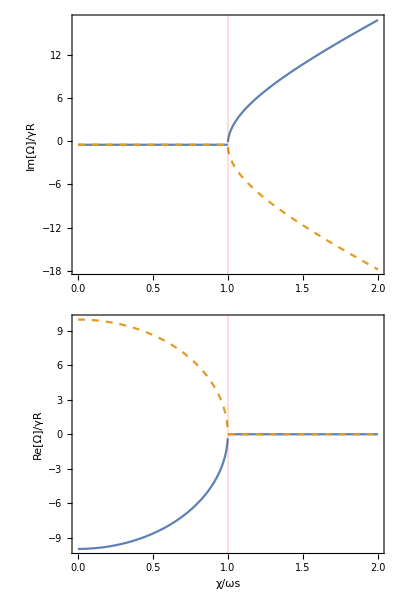

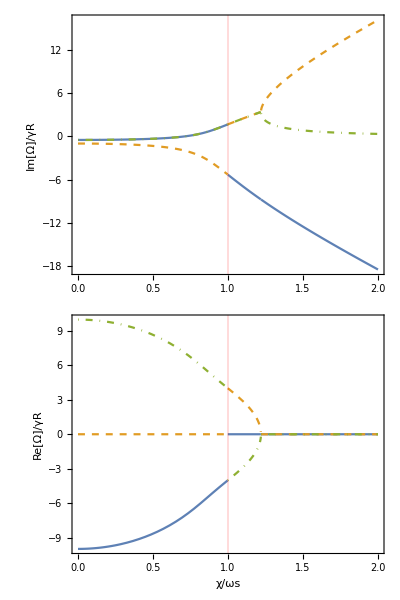

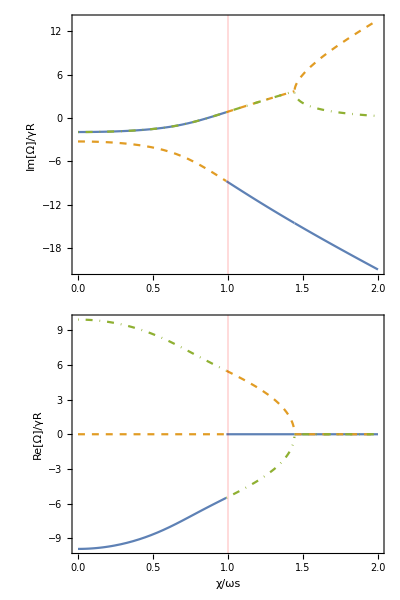

```mathematica
(*Checking stability*)
Clear[χ]
denominator=γbtot0-I Ω+κ0^2/(γa0-I Ω)-χ0^2/(γc0-I Ω);(*additional poles at γa,γc*)
Print["lossless: ",Solve[(denominator/.{γa0->0,γc0->0,γbtot0->γR0})==0,Ω]]
(*stabilitySol=Simplify[Solve[denominator==0,Ω],Assumptions->{κ0>0,χ0>0,γa0>0,γbtot0>0,γc0>0}];*)
denom[Tla_,Tlb_,Tlc_,symSRM_:False]:=γbtot[Tlb]-I Ω+ωs^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω);

stabilitysWLC[Tla_,Tlb_,Tlc_,symSRM_:False]:=(
sol=NSolve[denom[Tla,Tlb,Tlc,symSRM]==0,Ω];
p1=Plot[Evaluate[Table[(Im[Ω/.sol[[i]]]/.{χ->ratio ωs})/γR,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{1,All}},ImageSize->300,Frame->True,FrameLabel->{{"Im[Ω]/γR",},{,StringForm["poles of transfer function\nunstable when Im[Ω]≥0\nT_(l, a)=``, T_(l, b)=``, T_(l, c)=``, sym. SRM loss?=``",Tla,Tlb,Tlc,symSRM]}},GridLines->{{{1,Red}},None}];
p2=Plot[Evaluate[Table[(Re[Ω/.sol[[i]]]/.{χ->ratio ωs})/γR,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{All,1}},ImageSize->300,Frame->True,FrameLabel->{{"Re[Ω]/γR",},{"χ/ωs",}},GridLines->{{{1,Red}},None}];
Column[{p1,p2}])
(*Manipulate[stabilitysWLC[Tla,Tlb,Tlc],{Tla,0,1},{Tlb,0,1},{Tlc,0,1}]*)
(*If the Manipulate is not working, then run the cell again*)
(*Tla_,Tlb_,Tlc_*)
stabilitysWLC[0,0,0]
stabilitysWLC[0,0,0,True]
stabilitysWLC[0.1,0.1,0.1,True]
Clear[Tla,Tlb,Tlc]
(*realistically, γc is at least γR, so the lossless plot is not useful*)
```

```mathematica
(*sensitivity at 2.5 kHz versus squeezer parameter, like deg.int.sqz. plot,
symSRM=False throughout*)
(*
fProbe=2.5 10^3(*Hz*);
sensRef =ASDShsWLC[2π fProbe,0,0,0,0,0];

TlaList={0};
TlbList=Range[0,0.5,0.25];
TlcList={0};

Plot[Evaluate[Table[20Log10[ASDShsWLC[2π fProbe,2/τRoundTripSRC Log[10^(rdB/20)],TlaList[[i]],TlbList[[j]],TlcList[[k]],0]/sensRef]
,{i,1,Length[TlaList]},{j,1,Length[TlbList]},{k,1,Length[TlcList]}]],{rdB,0,5},PlotLegends->LineLegend[Flatten[Table[StringForm["T_(l, a)=``, T_(l, b)=``, T_(l, c)=``",TlaList[[i]],TlbList[[j]],TlcList[[k]]],{i,1,Length[TlaList]},{j,1,Length[TlbList]},{k,1,Length[TlcList]}]],LabelStyle->Directive[10]],Frame->True,FrameLabel->{{StringForm["strain sensitivity (NSR) in Hz^(-1/2) at `` kHz\nrelative to lossless, no squeezing value / dB",fProbe/10^3],},{"unitless squeezing, rdB=20 log_10(ⅇ^χFractionBox[τSRC, 2])","optical sWLC model\nκ=10γ_R, γ_R is SRM coupling rate\nno radiation pressure effects\nparameters of LIGO Voyager"}}]

(*showing that minimum is indeed χ=ωs*)
thresholdrdB = N[Minimize[{20Log10[ASDShsWLC[2π fProbe,2/τRoundTripSRC Log[10^(rdB/20)],0,0,0,0]/sensRef],rdB>0},{rdB}][[2]][[1]]]
thresholdχ=2/τRoundTripSRC Log[10^(rdB/20)]/.thresholdrdB;
tolerance=N[10^-5];
Print[StringForm["To a tolerance of ``, the optimum χ is on threshold: ``",ScientificForm[tolerance],Abs[(thresholdχ-ωs)/ωs]<tolerance]]
Print[StringForm["χOpti=``, ωs=``, χOpti/ωs=``",NumberForm[thresholdχ],NumberForm[N[ωs]],NumberForm[thresholdχ/N[ωs]]]]
(*Manipulate[LogLogPlot[ASDhPDLossy[2π f,χ=rat ωs,lossRatio=0,Rpd=0],{f,10,10^4},PlotRange->{10^-27,10^-22},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)",},{"frequency, f=Ω/(2 π) / Hz (log scale)",StringForm["above process optimises for sensitivity at `` kHz\nnot for overall bandwidth\nχ/ωs=``",fProbe/10^3,χ/ωs]}},GridLines->{{{fProbe,Red}},None}],{{rat,thresholdχ/N[ωs],"χ/ωs"},0,2}]*)
LogLogPlot[{
ASDShsWLC[2π f,(*χ=*)thresholdχ ,0,0,0,0],
ASDShsWLC[2π f,(*χ=*)ωs,0,0,0,0]},{f,10,10^4},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^-0.5 (log scale)",},{"frequency, f=Ω/(2 π) / Hz (log scale)",StringForm["sWLC - lossless\nabove process optimises for sensitivity at `` kHz\nnot for overall bandwidth",fProbe/10^3]}},GridLines->{{{fProbe,Red}},None},PlotLegends->{StringForm["χ=``ωs",NumberForm[thresholdχ/N[ωs],4]],"χ=ωs"}]
*)
```

```mathematica
(*to-do: figure what is going on with shot noise, why doesn't it appear unless γc≠0?*)
(*Sx2,out=1 for Tlc=0,
since everything is real, can use ComplexExpand,
since this is true for the NOPO case -- first understand that to understand this*)
Assumps={γR0>0,γa0≥0,Ω0>0,κ0>0,χ0>0,1≥Rpd0≥0,γbtot0>=γR0,γc0≥0};
Simplify[((1-Rpd0)(
ComplexExpand[Abs[γbtot0-2γR0-I Ω0+κ0^2/(γa0-I Ω0)-χ0^2/(γc0-I Ω0)]^2]
+ComplexExpand[Abs[(-2(γR0 γa0)^(1/2)κ0)/(γa0-I Ω0)]^2]
+ComplexExpand[Abs[-2(γR0 γb0)^(1/2)]^2]
+ComplexExpand[Abs[(2(γR0 γc0)^(1/2)χ0)/(γc0-I Ω0)]^2])/ComplexExpand[Abs[γbtot0-I Ω0+κ0^2/(γa0-I Ω0)-χ0^2/(γc0-I Ω0)]^2]+Rpd0)/.{γb0->γbtot0-γR0,γc0->0},Assumps]
```

1

```mathematica
(*splitting noise budget*)
RinsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=(1-Rpd)^(1/2)Abs[γbtot[Tlb]-2γR-I Ω+ωs^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]/Abs[γbtot[Tlb]-I Ω+ωs^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]
RlasWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=(1-Rpd)^(1/2)Abs[(-2(γR γa[Tla])^(1/2)ωs)/(γa[Tla]-I Ω)]/Abs[γbtot[Tlb]-I Ω+ωs^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]
RlbsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=(1-Rpd)^(1/2)Abs[-2(γR γb[Tlb])^(1/2)]/Abs[γbtot[Tlb]-I Ω+ωs^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]
RlcsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=(1-Rpd)^(1/2)Abs[(2(γR γc[Tlc,symSRM])^(1/2)χ)/(γc[Tlc,symSRM]-I Ω)]/Abs[γbtot[Tlb]-I Ω+ωs^2/(γa[Tla]-I Ω)-χ^2/(γc[Tlc,symSRM]-I Ω)]
RlpdsWLC[Ω_,χ_,Tla_,Tlb_,Tlc_,Rpd_,symSRM_:False]:=Rpd^(1/2)
(*RIntExtSqz=sum of above four in quadrature*)
(*https://mathematica.stackexchange.com/questions/10833/how-do-i-convert-an-argument-list-to-a-sequence-of-arguments
@@ is infix Apply[f,{a,b,c,d}]*)
plotNoiseBudgetsWLC[params_,symSRM_:False]:=
LogLinearPlot[{
20Log10[1],
20Log10[RinsWLC@@Join[{2π f},params,{symSRM}]],
20Log10[RlasWLC@@Join[{2π f},params,{symSRM}]],
20Log10[RlbsWLC@@Join[{2π f},params,{symSRM}]],
20Log10[RlcsWLC@@Join[{2π f},params,{symSRM}]],
20Log10[RlpdsWLC@@Join[{2π f},params,{symSRM}]],
20Log10[RsWLC@@Join[{2π f},params,{symSRM}]]},{f,10,10^4},PlotLegends->LineLegend[{"vacuum","R_in, behind SRM","(R^(L))_a, arm intra-cav.","(R^(L))_b, SRC signal intra-cav.","(R^(L))_c, SRC idler intra-cav.","(R^(L))_PD, PD loss","total shot noise"},LabelStyle->Directive[10],LegendLabel->labeller[params,symSRM]],PlotRange->All,PlotStyle->{Directive[Gray,Dashed],,,,,,Directive[Black,Dashed]},Frame->True,FrameLabel->{{"shot noise transfer function,\n|R| / dB (20log10)",},{"frequency, f=Ω/(2  π) / Hz","optical sWLC\nparameters of LIGO Voyager"}}]
```

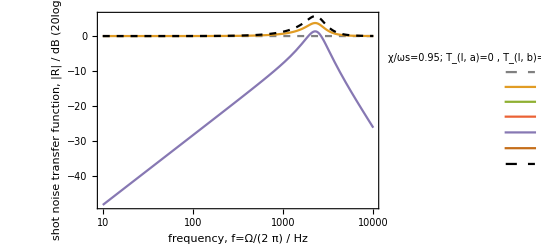

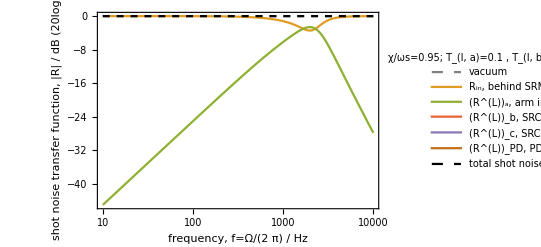

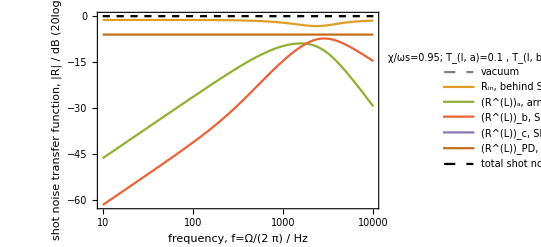

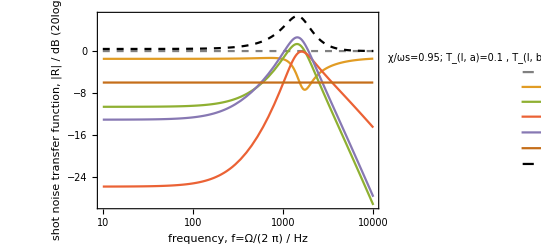

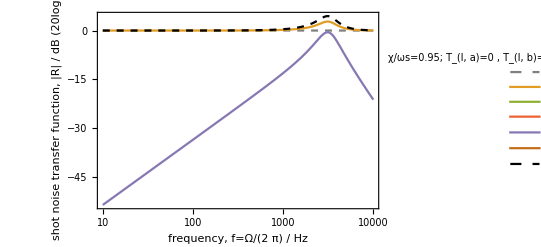

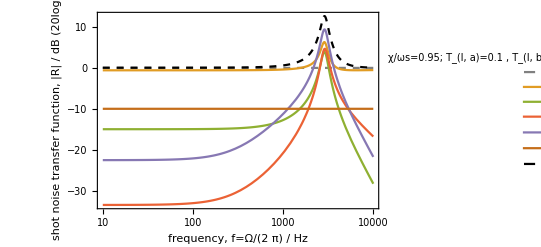

```mathematica
(*χ_,Tla_,Tlb_,Tlc_,Rpd_*)
χRatio0=0.95;
plotNoiseBudgetsWLC[{χRatio0 ωs,0,0,0,0},True]
plotNoiseBudgetsWLC[{χRatio0 ωs,0.1,0,0,0},False]
plotNoiseBudgetsWLC[{χRatio0 ωs,0.1,0.2,0,0.25},False]
plotNoiseBudgetsWLC[{χRatio0 ωs,0.1,0.2,0,0.25},True]
plotNoiseBudgetsWLC[{χRatio0 ωs,0,0,0.1,0},True]
plotNoiseBudgetsWLC[{χRatio0 ωs,0.1,0.1,0.1,0.1},True]
```

```mathematica
(*like deg. int. sqz. and degenerate OPO:
comparing shot noise to nondegenerate OPO variance in limit of arm cavity loss -> 1,
does the three mirror system reduce to a two mirror system of the SRM and ITM?*)

(*in limit of Tla->1*)
SX2out=Rpd1+(1-Rpd1)(
(γc1(γbtot1-2γR1)-Ω1^2-χ1^2)^2
+Ω1^2(γbtot1-2γR1+γc1)^2
+4 γR1 γb1 (γc1^2+Ω1^2)
+4 γR1 γc1 χ1^2
)/((γc1 γbtot1-Ω1^2-χ1^2)^2
+Ω1^2(γbtot1+γc1)^2);
Assumps3={γc1>=0,γR1>0,γbtot1>=γR1,Ω1>0,χ1>0};
FullSimplify[SX2out/.{γb1->γbtot1-γR1},Assumptions->Assumps3]
(*which agrees with NOPO (see calculation with asymmetric losses)!*)
```

1-(8 (-1+Rpd1) γc1 γR1 χ1^2)/((-γbtot1 γc1+χ1^2)^2+(γbtot1^2+γc1^2+2 χ1^2) Ω1^2+Ω1^4)

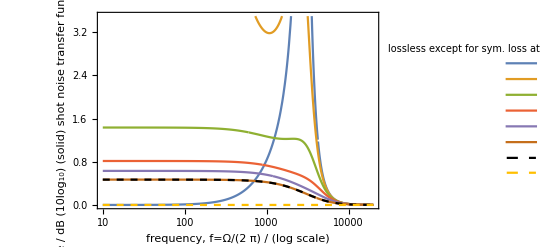

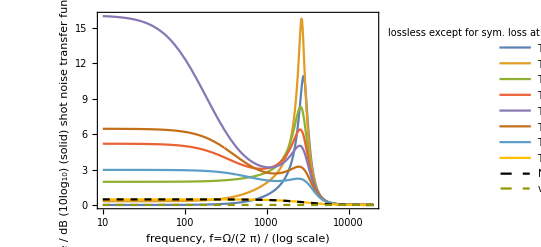

```mathematica
(*to match original NOPO calculation, need symmetric losses γc=γbot=γR+γb
have now shown that asymmetric losses also matches.
therefore, should have γctot=γR+γc where γc is now the added loss (i.e. making the SRM loss symmetric) -- we have shown in the NOPO case that we are free to split the loss like this as long as we only care about detecting b mode at the output*)
NOPOV22symSRM[Ω_,g_,Tlb_:0,Tlc_:0,Rpd_:0]:=(
(*looking at formal limit of Tla->1, noise in the â mode also shuts off
-- the equivalent of making Titm perfect, not a vacuum port
-- why isn't power still lost through Titm, term vanishes with â?*)
κaf=γR;(*uses Tse and Lse*)
κar=0;
κal=γb[Tlb];
κa=κaf+κar+κal;(*γbtot[Tloss]*)
(*assuming that the SRM loss is symmetric between b and c, else the variance is just 1*)
κc=γc[Tlc,True];(*γctot[Tlc]=γR+γc0[Tlc]*)
(*this formula is agnostic towards where the ĉ noise originates*)
1+(8 (1-Rpd) κaf κc Abs[g]^2)/((κa κc-Abs[g]^2)^2+Ω^2 (κa^2+κc^2+2 Abs[g]^2)+Ω^4)) 

(*plotting*)
χRatio0=0.85;
plotArmLossLimitSymSrm[armLossList_,plotRange_:Automatic]:=
LogLinearPlot[Evaluate[Join[
Table[
20Log10[RsWLC[2π f,χRatio0 ωs,armLossList[[i]],0,0,0,True]](*symSRM=True to match NOPO*)
,{i,1,Length[armLossList]}],
{10Log10[NOPOV22symSRM[2π f,χRatio0 ωs]],
10Log10[1]}]],
{f,10,2 10^4},PlotRange->plotRange,PlotLegends->LineLegend[Join[
Table[StringForm["T_(l, a)=``",N[armLossList[[i]]]]
,{i,1,Length[armLossList]}],
{"NOPO V_22","vacuum"}],LabelStyle->Directive[10],LegendLabel->StringForm["lossless except for sym. loss at SRM\nlast loss is T_(l, a)=1-``",ScientificForm[N[ϵ]]]],PlotStyle->Join[Table[{,},{i,1,Length[armLossList]}],{Directive[Black,Dashed],Dashed}],Frame->True,FrameLabel->{{ "(dashed) variance / dB (10log_10)\n(solid) shot noise transfer function\n|R| / dB (20log_10)",},{"frequency, f=Ω/(2  π) / (log scale)","sWLC reducing to nondegenerate OPO when T_(l, a)->1\nusing parameters of reduced two-mirror system (SRM and ITM)\nbut with T_ITM=0 as entire â mode vanishes\nassuming symmetric loss at SRM, i.e. γctot=γR+γc≠0"}}]
ϵ=10^-100;
armLossList=Join[Range[0,0.9,0.2],{1-ϵ}];
plotArmLossLimitSymSrm[armLossList]
plotArmLossLimitSymSrm[Join[{0,0.1,0.15,0.175,0.2,0.25,0.3},{1-ϵ}],All]
```

```mathematica
(*want to find threshold, analytically optimising for it is hard*)
```

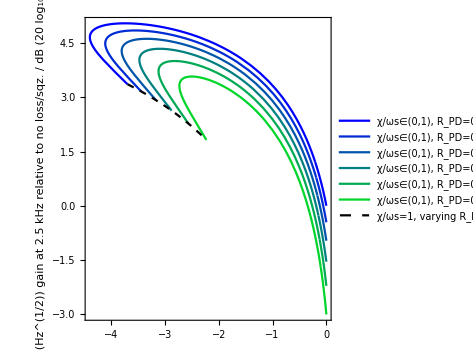
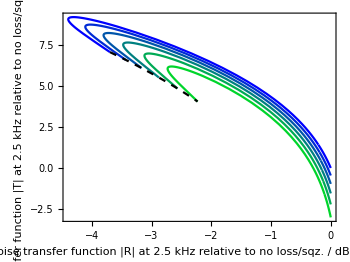

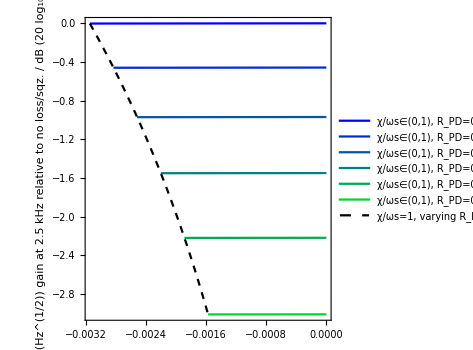
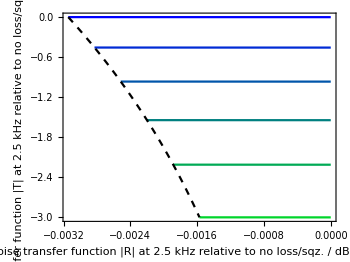

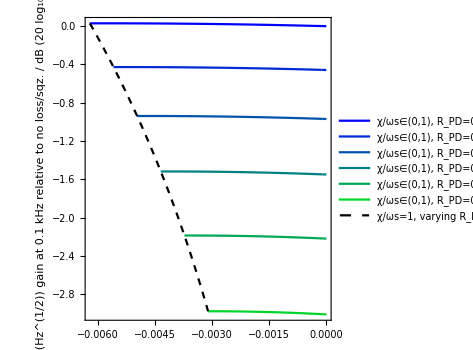
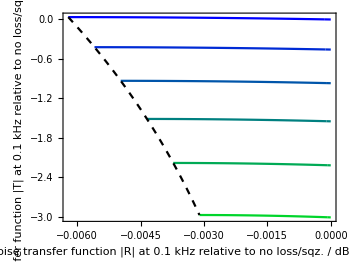

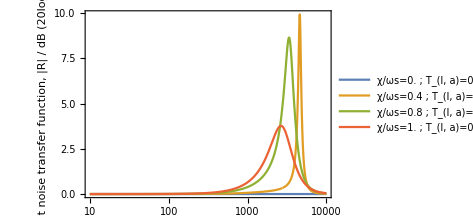
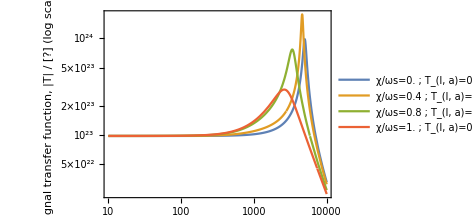

```mathematica
(*threshold finding plot -- copied from deg int sqz .nb*)
Clear[plotThresholdFinder,fProbe]
plotThresholdFinder[fProbe_,Tlc_,symSRM_:False,pastThreshold_:False]:=(
rpdList=Subdivide[0,0.5,5];
(*fProbe=2.5 10^3(*Hz*);*)
probeNoiseRef=RsWLC[2π fProbe,0,0,0,0,0];
probeSigRef=TsWLC[2π fProbe,0,0,0,0,0];
probeSensRef=ASDShsWLC[2π fProbe,0,0,0,0,0];
p1=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[RsWLC[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],symSRM]/probeNoiseRef],-20Log10[ASDShsWLC[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],symSRM]/probeSensRef]}},{i,1,Length[rpdList]}],1]],{χRatio,0,1},Frame->True,FrameLabel->{{StringForm["SNR (Hz^(1/2)) gain at `` kHz\nrelative to no loss/sqz. / dB (20 log_10(1/S_h))",N[fProbe/10^3]],},{,"optical stable WLC\nno radiation pressure effects\nparameters of LIGO Voyager"}},PlotStyle->Table[Blend[{Blue,Green},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/ωs∈(0,1), R_PD=``",NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10],LegendLabel->StringForm["T_(l, c)=``",NumberForm[N[Tlc]]]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,AspectRatio->1];
p2=ParametricPlot[{
{-20Log10[RsWLC[2π fProbe,1ωs,0,0,Tlc,Rpd,symSRM]/probeNoiseRef],-20Log10[ASDShsWLC[2π fProbe,1ωs,0,0,Tlc,Rpd,symSRM]/probeSensRef]}},{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{StringForm["χ/ωs=1, varying R_PD∈(``,``)",NumberForm[N[rpdList[[1]]]],NumberForm[N[rpdList[[-1]]]]]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350];
If[pastThreshold,
p1b=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[RsWLC[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],symSRM]/probeNoiseRef],-20Log10[ASDShsWLC[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],symSRM]/probeSensRef]}},{i,1,Length[rpdList]}],1]],{χRatio,1,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/ωs∈(1,2), R_PD=``",NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350];
p1and2=Show[p1,p1b,p2];,
p1and2=Show[p1,p2];];
p3=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[RsWLC[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],symSRM]/probeNoiseRef],20Log10[TsWLC[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],symSRM]/probeSigRef]}},{i,1,Length[rpdList]}],1]],{χRatio,0,1},Frame->True,FrameLabel->{{StringForm["signal transfer function |T| at `` kHz\nrelative to no loss/sqz. / dB (20 log_10)",N[fProbe/10^3]],},{StringForm["noise transfer function |R| at `` kHz\nrelative to no loss/sqz. / dB (-20 log_10)",N[fProbe/10^3]],}},PlotStyle->Table[Blend[{Blue,Green},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{80,10},{All,1}},ImageSize->350,AspectRatio->3/4];
p4=ParametricPlot[
{-20Log10[RsWLC[2π fProbe,1ωs,0,0,Tlc,Rpd,symSRM]/probeNoiseRef],
20Log10[TsWLC[2π fProbe,1ωs,0,0,Tlc,Rpd,symSRM]/probeSigRef]},{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black,Dashed],PlotRange->All,ImagePadding->{{80,10},{All,1}}];
If[pastThreshold,
p3b=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[RsWLC[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],symSRM]/probeNoiseRef],20Log10[TsWLC[2π fProbe,χRatio ωs,0,0,Tlc,rpdList[[i]],symSRM]/probeSigRef]}},{i,1,Length[rpdList]}],1]],{χRatio,1,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350];
p3and4=Show[p3,p3b,p4];,
p3and4=Show[p3,p4];];
Column[{p1and2,p3and4},Spacings->0])
(*fProbe_,Tlc_,symSRM_:False,pastThreshold_:False*)
plotThresholdFinder[2.5 10^3(*Hz*),0.1]
plotThresholdFinder[2.5 10^3(*Hz*),1-10^-100]
plotThresholdFinder[100(*Hz*),0.1]
plotsWLC[{
{0,0,0,0.1,0},
{0.4ωs,0,0,0.1,0},
{0.8ωs,0,0,0.1,0},
{1ωs,0,0,0.1,0}}](*γc->∞ makes T no longer depend on χ*)
```

```mathematica
(*trying to find a solution for threshold, i.e. extremum of shot noise*)
$Assumptions={Ω>0,γa≥0,γbtot≥γR>0,γc≥0,1>Rpd≥0,χ≥0,ωs>0};
Print[FullSimplify[((1-Rpd)(
ComplexExpand[Abs[γbtot-2γR-I Ω+ωs^2/(γa-I Ω)-χ^2/(γc-I Ω)]^2]
+ComplexExpand[Abs[(-2(γR γa)^(1/2)ωs)/(γa-I Ω)]^2]
+ComplexExpand[Abs[-2(γR γb)^(1/2)]^2]
+ComplexExpand[Abs[(2(γR γc)^(1/2)χ)/(γc-I Ω)]^2])/ComplexExpand[Abs[γbtot-I Ω+ωs^2/(γa-I Ω)-χ^2/(γc-I Ω)]^2]+Rpd)/.{γb->γbtot-γR}]]
Sx1[Ω_,χ_]:=((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)
```

((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)

```mathematica
(*gradient for manual analytic solution*)
Print[{D[Sx1[Ω,χ],Ω]//FullSimplify,D[Sx1[Ω,χ],χ]//FullSimplify}]
DΩSx[Ω_,χ_]:=(16 (-1+Rpd) γc γR χ^2 Ω ((γa^2+Ω^2)^2 (γbtot^2+γc^2+2 (χ^2+Ω^2))+2 (γa^3 γbtot+γa γc (-γbtot γc+χ^2)-Ω^4-γa^2 (γc^2+χ^2+2 Ω^2)) ωs^2+(γa-γc) (γa+γc) ωs^4))/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2
DχSx[Ω_,χ_]:=-((16 (-1+Rpd) γc γR χ (γa^2+Ω^2) ((γa^2+Ω^2) (-χ^4+(γbtot^2+Ω^2) (γc^2+Ω^2))+2 (γa γbtot-Ω^2) (γc^2+Ω^2) ωs^2+(γc^2+Ω^2) ωs^4))/((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2)
GradSx[Ω_,χ_]:={DΩSx[Ω,χ],DχSx[Ω,χ]}
```

```mathematica
(*denominator of Sx*)
Collect[Denominator[Sx1[Ω,χ]],Ω,FullSimplify]
%/.{Ω->0,ωs->0}//Simplify
```

Ω^6+Ω^4 (γa^2+γbtot^2+γc^2+2 χ^2-2 ωs^2)+(γa γbtot γc-γa χ^2+γc ωs^2)^2+Ω^2 ((-γbtot γc+χ^2)^2+γa^2 (γbtot^2+γc^2+2 χ^2)+2 γa γbtot ωs^2-2 (γc^2+χ^2) ωs^2+ωs^4)

(γa γbtot γc-γa χ^2)^2

```mathematica
GradSx[0,χ]/.γa->0
```

{0,0}

```mathematica
(*Derivative diverges at threshold, watch out*)
Limit[Sx1[Ω,χ],γa->∞]//FullSimplify
```

1-(8 (-1+Rpd) γc γR χ^2)/((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)

```mathematica
Limit[GradSx[Ω,χ],γa->0]//Simplify
Limit[GradSx[Ω,χ],γa->∞]//Simplify
```

{(16 (-1+Rpd) γc γR χ^2 Ω (Ω^4 (γbtot^2+γc^2+2 (χ^2+Ω^2))-2 Ω^4 ωs^2-γc^2 ωs^4))/(((-γbtot γc+χ^2)^2 Ω^2+(γbtot^2+γc^2+2 χ^2) Ω^4+Ω^6-2 Ω^2 (γc^2+χ^2+Ω^2) ωs^2+(γc^2+Ω^2) ωs^4)^2),-(16 (-1+Rpd) γc γR χ Ω^2 (-χ^4 Ω^2+γbtot^2 Ω^2 (γc^2+Ω^2)+(γc^2+Ω^2) (Ω^2-ωs^2)^2))/((-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γbtot^2 Ω^2 (γc^2+Ω^2)+(γc^2+Ω^2) (Ω^2-ωs^2)^2+2 χ^2 (Ω^4-Ω^2 ωs^2))^2)}

{(16 (-1+Rpd) γc γR χ^2 Ω (γbtot^2+γc^2+2 (χ^2+Ω^2)))/((-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))^2),-(16 (-1+Rpd) γc γR χ (-χ^4+γc^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2)))/((-2 γbtot γc χ^2+χ^4+γc^2 Ω^2+2 χ^2 Ω^2+Ω^4+γbtot^2 (γc^2+Ω^2))^2)}

```mathematica
(*solution to threshold points*)
sol=NSolve[{GradSx[Ω,χ]=={0,0},Ω≥0,χ≥0,γbtot≥γR>0,ωs>0,γa≥0,γc≥0,1>Rpd≥0},{Ω,χ}];
If[Head[sol]≠Symbol&&Head[sol]==List,Print["Solve[..., {Ω,χ}] found "<>ToString[Length[sol]]<>" solutions"]]
```

$Aborted

```mathematica
Sx1[Ω,χ]/.{γbtot->γR,γa->0,Rpd->0}//FullSimplify
Collect[-2 γc γR χ^2 Ω^2+γc^2 (γR^2 Ω^2+(Ω^2-ωs^2)^2)+Ω^2 (γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2),Ω]
GradSx[Ω,χ]/.{γbtot->γR,γa->0,Rpd->0}//FullSimplify
```

1+(8 γc γR χ^2 Ω^2)/(-2 γc γR χ^2 Ω^2+γc^2 (γR^2 Ω^2+(Ω^2-ωs^2)^2)+Ω^2 (γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2))

Ω^6+γc^2 ωs^4+Ω^4 (γc^2+γR^2+2 χ^2-2 ωs^2)+Ω^2 (γc^2 γR^2-2 γc γR χ^2+χ^4-2 γc^2 ωs^2-2 χ^2 ωs^2+ωs^4)

{-(16 γc γR χ^2 Ω (γc^2 (Ω^4-ωs^4)+Ω^4 (γR^2+2 (χ^2+Ω^2-ωs^2))))/((-2 γc γR χ^2 Ω^2+γc^2 (γR^2 Ω^2+(Ω^2-ωs^2)^2)+Ω^2 (γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2))^2),(16 γc γR χ Ω^2 (Ω^2 (-χ^4+(γc^2+Ω^2) (γR^2+Ω^2))-2 Ω^2 (γc^2+Ω^2) ωs^2+(γc^2+Ω^2) ωs^4))/((-2 γc γR χ^2 Ω^2+γc^2 (γR^2 Ω^2+(Ω^2-ωs^2)^2)+Ω^2 (γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2))^2)}

```mathematica
(*plotting threshold points*)
(*parameters of LIGO Voyager from Li et al 2020*)
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);
Larm=4. 10^3(*m*);
Pcirc=3. 10^6(*W*);
λ0=2. 10^-6(*m*);
ω0=2π c/λ0;
γR=2π 500.(*Hz*);
ωs=10γR;
τRoundTripArm=(2 Larm)/c;
Tsrm=0.046;
τRoundTripSRC=-1/(2 γR)Log[1-Tsrm];
γaFn[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
γbtotFn[Tlb_]:=γR+-1/(2 τRoundTripSRC)Log[1-Tlb]
γcFn[Tlc_]:=-1/(2 τRoundTripSRC)Log[1-Tlc]
```

```mathematica
(*one loss at a time, here's with γc turned on*)
γc=γcFn[10^-3];
sol=Solve[{(GradSx[Ω,χ]/.{γbtot->γR,γa->0,Rpd->0})=={0,0},Ω≥0,χ≥0,γc>0},{Ω,χ}]
pointSol=Select[sol,(Length[#]==2)&]
{Ω/ωs,χ/γbtotFn[0]}/.pointSol
```

{{χ→ConditionalExpression[0,0<Ω<4531.29||Ω>4531.29]},{Ω→ConditionalExpression[0,χ≥0]},{Ω→4531.29,χ→0},{Ω→4531.29,χ→31090.8}}

{{Ω→4531.29,χ→0},{Ω→4531.29,χ→31090.8}}

{{0.144235,0.},{0.144235,9.89651}}

```mathematica
(*FindRoot[{(GradSx[Ω,χ]/.{γbtot->γR,γa->0,Rpd->0})=={0,0}},{Ω,13175},{χ,28556}]*)
```

```mathematica
(*to-do: figure out why Solve returns solutions when NSolve doesn't
also, switch over to using native maximisers instead of manually finding ∇Sx
*)
(*Maximize[{Sx1[Ω,χ],Ω≥0,γa≥0,γbtot≥γR>0,γc≥0,1>Rpd≥0,χ≥0,ωs>0},{Ω,χ},Reals,WorkingPrecision->5]//Timing*)
```

```mathematica
(*poles*)
sol=Solve[Denominator[Sx1[Ω,χ]]==0,{Ω,χ}];
(*manually filtering for Ω≥0,χ≥0*)
maybeRealPoles=sol[[2;;4;;2]];
Block[{γa=0,γc=γcFn[0.05],γbtot=γR},
(*just looking at one pole for now, suspect other is symmetric is some way*)
noIm=NMinimize[{Abs[Im[χ/.maybeRealPoles[[1]]]],Ω≥0},Ω];
{Ω0,χ0}={Ω/.noIm[[2]],(χ/.maybeRealPoles[[1]])/.Ω->Ω/.noIm[[2]]};
Print[StringForm["`` ``",Ω0/(2π),χ0/ωs]];
Print[Sx1[Ω0,χ0]/.Rpd->0,20 1/2 Log10[Sx1[Ω0,χ0]/.Rpd->0]]
]
(*looks like there are real poles for χ<ωs (if we consider 3 10^14 to likely indicate a pole), consider these threshold?*)
(*to-do: if these are poles, then why don't they appear in the Sx plots from before? or are they just very large dB values -- not actual poles?
also, doesn't physically make sense to have poles in lossy case -- surely

could the poles just be very large and numerical error is causing problems i.e. overflow?*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

3610.24 0.699671

3.11133×10^14144.929

Power::infy: Infinite expression 1/0. encountered.

NMaximize::nnum: The function value -∞ is not a number at {f,χRatio} = {3342.7,0.753427}.

{144.904,{f→3342.7,χRatio→0.753427}}

23669.6

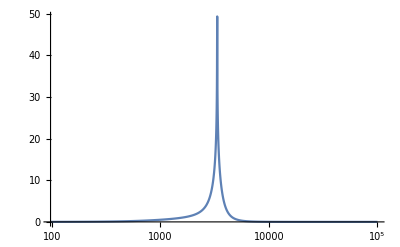

Power::infy: Infinite expression 1/0. encountered.

NMaximize::nnum: The function value -∞ is not a number at {f,χRatio} = {3438.47,0.73505}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NMaximize::nnum: The function value -∞ is not a number at {f,χRatio} = {3008.16,0.810624}.

NMaximize::nrnum: The function value -143.718-13.6438 ⅈ is not a real number at {f,χRatio} = {2473.29,0.883456}.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

NMaximize::nnum: The function value -∞ is not a number at {f,χRatio} = {2.5649×10^-6,0.633608}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NMaximize::nrnum: The function value -152.31-13.6438 ⅈ is not a real number at {f,χRatio} = {6.06456×10^-6,0.401642}.

NMaximize::nrnum: The function value -153.454-13.6438 ⅈ is not a real number at {f,χRatio} = {3.13396×10^-6,0.359927}.

General::stop: Further output of NMaximize::nrnum will be suppressed during this calculation.

-Graphics-

```mathematica
(*to-do: try to decrease WorkingPrecision?*)
γa=γaFn[0.01];
γbtot=γbtotFn[0.01];
γc=γcFn[0.05];
Rpd=0;
maybePole=NMaximize[{20 1/2 Log10[Sx1[2π f,χRatio ωs]],0≤f≤10^5,0≤χRatio≤1},{f,χRatio}]
χ0=(χRatio/.maybePole[[2]]) ωs
LogLinearPlot[20 1/2 Log10[Sx1[2π f,χ0]],{f,0,10^5},PlotRange->All]
Plot[Block[{γa=γaFn[Tla]},NMaximize[{20Log10[Sx1[2π f,χRatio ωs]^(1/2)],0≤f<10^5,0≤χRatio≤1},{f,χRatio}]],{Tla,0,1},PerformanceGoal->"Speed",AspectRatio->1,PlotRange->All,Frame->True]
Clear[γa,γbtot,γc,Rpd]
```

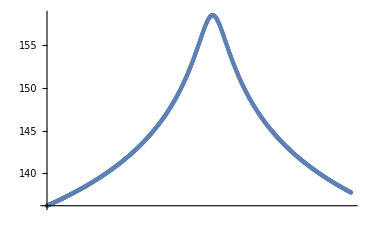

```mathematica
(*must be numerical error? close inspection of the peak shows it to be finite, not a pole*)
f0=f/.maybePole[[2]];
pm=10^-3/9;
LogLinearPlot[20Log10[RsWLC[2π f,χ0,0.01,0.01,0.05,0]],{f,f0-pm,f0+pm},PlotRange->All,PlotPoints->1000,Mesh->All]
```

```mathematica
NSolve[{Denominator[Sx1[Ω,χ]]==0,Ω≥0},{Ω,χ}];
%//Simplify
```

$Aborted

$Aborted

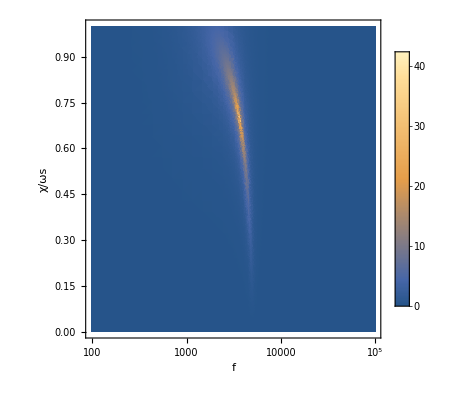

NMaximize::nrnum: The function value -141.919-13.6438 ⅈ is not a real number at {f,χRatio} = {3610.24,0.699671}.

{144.929,{f→3610.24,χRatio→0.699671}}

{10.6644,{f→2843.04}}

{1.,{f→1.54761}}

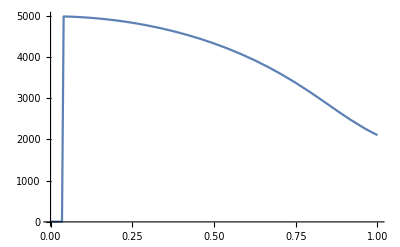

```mathematica
γa=γaFn[0];
γbtot=γbtotFn[0];
γc=γcFn[0.05];
Rpd=0;
DensityPlot[20Log10[Sx1[2π f,χRatio ωs]^(1/2)],{f,0,10^5},{χRatio,0,1},PlotLegends->Automatic,Frame->True,FrameLabel->{{"χ/ωs",},{"f",}},ScalingFunctions->{"Log",None},PlotRange->All,MaxRecursion->5]
NMaximize[{20Log10[Sx1[2π f,χRatio ωs]^(1/2)],10^5≥f≥0,1≥χRatio≥0},{f,χRatio}]

NMaximize[{Sx1[2π f,0.85ωs],f≥0},f]
FindMaximum[{Sx1[2π f,0.85ωs],f≥0},f]
Plot[f/.NMaximize[{Sx1[2π f,ratio ωs],f≥0},f][[2]],{ratio,0,1},PerformanceGoal->"Speed"]
(*
FindMaximum[{Sx1[2π f,0.01 ωs],f≥0},f]
Plot[Sx1[2π f,0.01 ωs],{f,0,10^4},PlotRange->All]
*)
Clear[γa,γbtot,γc,Rpd]
```

```mathematica
Clear[γc]
sol=Solve[{(GradSx[Ω,χ]/.{γbtot->γR,γa->0,Rpd->0})=={0,0},Ω≥0,χ≥0,γc>0},{Ω,χ}];
pointSol=Select[sol,(Length[#]==2)&];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.,{Ω→2.582503249,χ→1.075682708}}

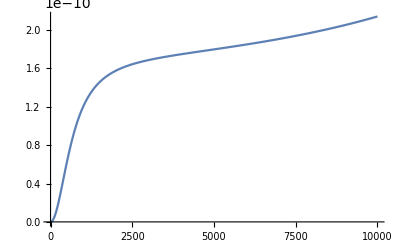

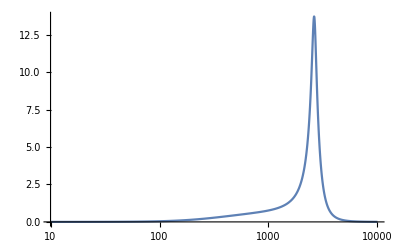

```mathematica
γa=0;
γbtot=γR;
γc=γcFn[0.01];
Rpd=0;
NMaximize[{Sx1[Ω,χ],Ω≥0,χ≥0},{Ω,χ},WorkingPrecision->10]
Plot[20Log10[Sx1[Ω,χ/.%[[2]]]],{Ω,0,10^4},PlotRange->All,GridLines->{{Ω/.%[[2]]},{}}]
LogLinearPlot[20Log10[Sx1[2π f,0.85ωs]^(1/2)],{f,10,10^4},PlotRange->All]
Clear[γa,γbtot,γc,Rpd]
```

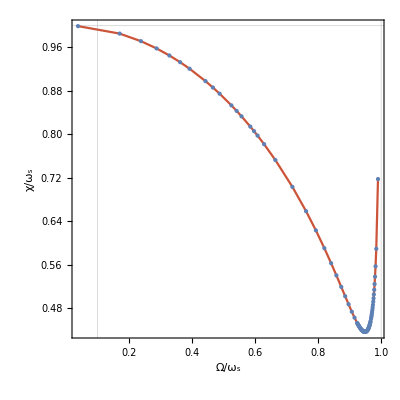

```mathematica
(*plotting one solution -- using Solve on Gradient==0 rather than native optimisation*)
Clear[γbtot,γa]
ParametricPlot[Block[{γc=γaFn[Tlc]},{Ω/ωs,χ/ωs}/.Solve[{(GradSx[Ω,χ]/.{γbtot->γR,γa->0,Rpd->0})=={0,0},Ω≥0,χ≥0},{Ω,χ}][[-1]]],
{Tlc,0,1},PerformanceGoal->"Speed",AspectRatio->1,PlotRange->All,Frame->True,FrameLabel->{{"χ/ω_s",},{"Ω/ω_s",StringForm["nondegenerate internal squeezing\nparameters of LIGO Voyager\nthreshold points, i.e. extrema of S_x(Ω,χ) (shot noise)\nas a function of T_(l, c)∈(0,1)\nT_(l, a)=0, T_(l, b)=``, R_PD=``",0,0]}},GridLines->{{0,0.1,1},{1}},ColorFunction->"Rainbow",Mesh->All]
```

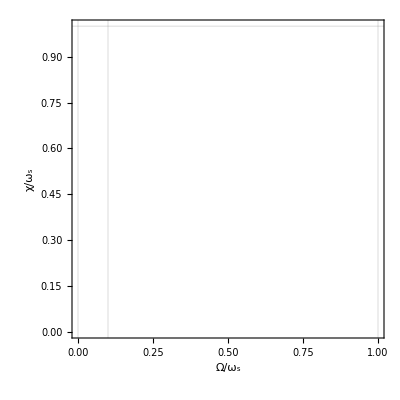

```mathematica
(*should be using NSolve for numerical solutions, Solve could be inaccurate?*)
(*to-do: why doesn't finding the sol separately instead of for each point not work?*)
Clear[γc]
sol=Solve[{(GradSx[Ω,χ]/.{γbtot->γR,γa->0,Rpd->0})=={0,0},Ω≥0,χ≥0,γc>0},{Ω,χ}];
ParametricPlot[Block[{γc=γcFn[Tlc]},{Ω/ωs,χ/ωs}/.sol[[-1]]],
{Tlc,0,1},PerformanceGoal->"Speed",AspectRatio->1,PlotRange->{{0,All},All},Frame->True,FrameLabel->{{"χ/ω_s",},{"Ω/ω_s",StringForm["nondegenerate internal squeezing\nparameters of LIGO Voyager\nthreshold points, i.e. extrema of S_x(Ω,χ) (shot noise)\nas a function of T_(l, c)∈(0,1)\nT_(l, a)=``, T_(l, b)=``, R_PD=``",0,0,0]}},GridLines->{{0,0.1,1},{1}},ColorFunction->"Rainbow",Mesh->All]
```

```mathematica
(*two peaks?*)
Clear[γa]
γa=γaFn[0.5];
Tlb0=0;
γbtot=γbtotFn[Tlb0];
Tlc0=1. 10^-2;
γc=γcFn[Tlc0];
NSolve[{(GradSx[Ω,χ]/.{Rpd->0})=={0,0},Ω≥0,χ≥0},{Ω,χ},Reals]
```

{{χ→25146.3,Ω→15978.8},{χ→24493.1,Ω→11096.8}}

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

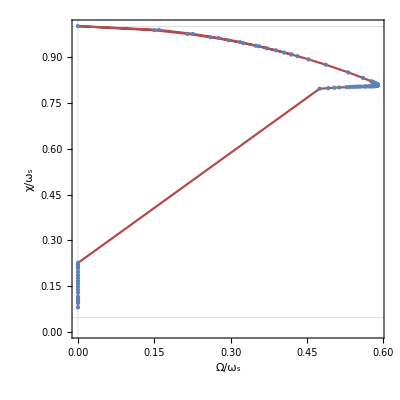

```mathematica
Tlb0=0;
γbtot=γbtotFn[Tlb0];
Tlc0=1. 10^-2;
γc=γcFn[Tlc0];
ParametricPlot[Block[{γa=γaFn[Tla]},{Ω/ωs,χ/ωs}/.Solve[{(GradSx[Ω,χ]/.{Rpd->0})=={0,0},Ω≥0,χ≥0},{Ω,χ}][[-1]]],
{Tla,0,1},PerformanceGoal->"Speed",AspectRatio->1,PlotRange->{Automatic,{0,Automatic}},Frame->True,FrameLabel->{{"χ/ω_s",},{"Ω/ω_s",StringForm["nondegenerate internal squeezing\nparameters of LIGO Voyager\nthreshold points, i.e. extrema of S_x(Ω,χ) (shot noise)\nas a function of T_(l, a)∈(0,1)\nT_(l, b)=``, T_(l, c)=``, R_PD=``",Tlb0,Tlc0,0]}},GridLines->{{0,1},{1,1/ωs(γbtot γc)^(1/2)}},ColorFunction->"Rainbow",Mesh->All]
Clear[γbtot,γc]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

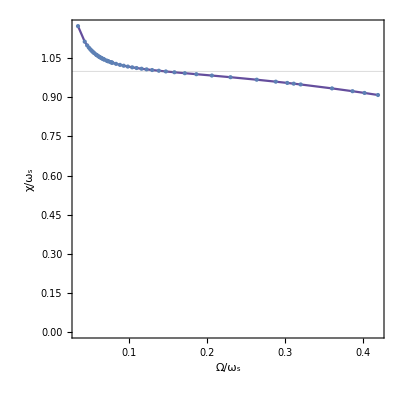

```mathematica
Tla0=0;
γa=γaFn[Tla0];
Tlc0=1. 10^-2;
γc=γcFn[Tlc0];
ParametricPlot[Block[{γbtot=γbtotFn[Tlb]},{Ω/ωs,χ/ωs}/.Solve[{(GradSx[Ω,χ]/.{Rpd->0})=={0,0},Ω≥0,χ≥0},{Ω,χ}][[-1]]],
{Tlb,0,1},PerformanceGoal->"Speed",AspectRatio->1,PlotRange->{Automatic,{0,Automatic}},Frame->True,FrameLabel->{{"χ/ω_s",},{"Ω/ω_s",StringForm["nondegenerate internal squeezing\nparameters of LIGO Voyager\nthreshold points, i.e. extrema of S_x(Ω,χ) (shot noise)\nas a function of T_(l, b)∈(0,1)\nT_(l, a)=``, T_(l, c)=``, R_PD=``",Tla0,Tlc0,0]}},GridLines->{{0,1},{1}},ColorFunction->"Rainbow",Mesh->All]
Clear[γa,γc]
```